```mathematica
Gg=6.674*10^-11;
OneYear=31557600;
Msun=1.989*10^30;
Pnames={"Earth","Mars"};
Pmass={5.9722*10^24,6.4169*10^23};
Peccen={0.01671123,0.0933941};
```

```mathematica
(* Orbit simulation equations - 2D.  This will be used for the test simulations involving "sun", "mercury", "venus" etc. *)
rdist[ptx_,pty_,psx_,psy_]:=((ptx-psx)^2+(pty-psy)^2)^(1/2);
(*total force*)Ftot[ptm_,ptx_,pty_,psm_,psx_,psy_]:=-(G *ptm *psm)/rdist[ptx,pty,psx,psy]^2 ;
(*x/y force components*)Fxx[ptm_,ptx_,pty_,psm_,psx_,psy_]:=Ftot[ptm,ptx,pty,psm,psx,psy](ptx-psx)/rdist[ptx,pty,psx,psy];
Fyy[ptm_,ptx_,pty_,psm_,psx_,psy_]:=Ftot[ptm,ptx,pty,psm,psx,psy](pty-psy)/rdist[ptx,pty,psx,psy];
ma=1;xa=2;ya=3;
Fx[pT_,pS_]:=Fxx[pT⟦ma⟧,pT⟦xa⟧,pT⟦ya⟧,pS⟦ma⟧,pS⟦xa⟧,pS⟦ya⟧];
Fy[pT_,pS_]:=Fyy[pT⟦ma⟧,pT⟦xa⟧,pT⟦ya⟧,pS⟦ma⟧,pS⟦xa⟧,pS⟦ya⟧];
(*x/y acceleration components, as vectors*)Ax[pT_,pS_]:=Fx[pT,pS]/pT⟦ma⟧;
Ay[pT_,pS_]:=Fy[pT,pS]/pT⟦ma⟧;
```

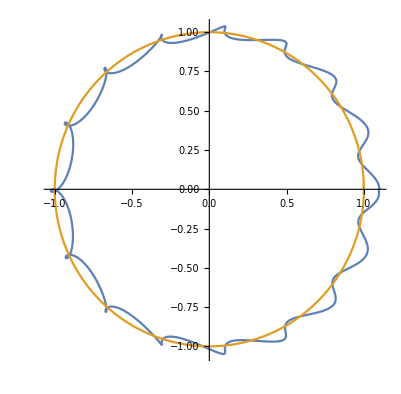

```mathematica
M0=50;M1=0.001;M2=2;
Pc0={M0,0,0};
Pc1={M1,x1[t],y1[t]};
Pc2={M2,R2 *Cos[V2/R2*t],R2 *Sin[V2/R2*t]};
G=1;R1=1.1;R2=1;e2=0.016;V1=√((G *M2)/(R1-R2));V2=√((1+e2)*(G *M0)/R1);result=NDSolve[{ x1''[t]==Ax[Pc1,Pc0]+Ax[Pc1,Pc2], y1''[t]==Ay[Pc1,Pc0]+Ay[Pc1,Pc2],x1[0]==R1,y1[0]==0,x1'[0]==0,y1'[0]==V1},{x1,y1},{t,0,Per},MaxSteps->Infinity];
ParametricPlot[{Evaluate[{x1[t],y1[t]}/.result],Evaluate[{Pc2[[2]],Pc2[[3]]}/.result]},{t,0,0.93},AspectRatio->Automatic,PlotPoints->500,PlotRange->Automatic]
```

```mathematica
fx[t_]:=Evaluate[x1[t]/.result]
fy[t_]:=Evaluate[y1[t]/.result]
fvx[t_]:=Evaluate[x1'[t]/.result]
fvy[t_]:=Evaluate[y1'[t]/.result]
```

```mathematica
Solve[fy[t]==0,t]
fy[0.459]
fy[0.93]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.454819}}

{-0.0154742}

{0.00582768}

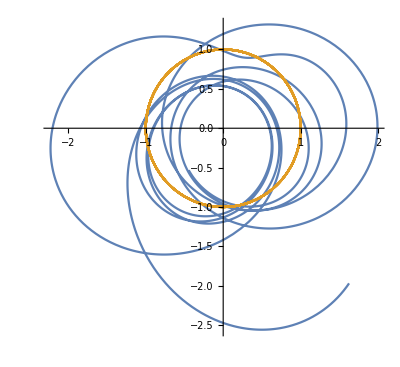

```mathematica
result2=NDSolve[{ x1''[t]==Ax[Pc1,Pc0]+Ax[Pc1,Pc2], y1''[t]==Ay[Pc1,Pc0]+Ay[Pc1,Pc2],x1[0]==fx[1][[1]],y1[0]==fy[1][[1]],x1'[0]==fvx[1][[1]],y1'[0]==fvy[1][[1]]},{x1,y1},{t,1,10},MaxSteps->Infinity];
ParametricPlot[{Evaluate[{x1[t],y1[t]}/.result2],Evaluate[{Pc2[[2]],Pc2[[3]]}/.result2]},{t,1,10},AspectRatio->Automatic,PlotPoints->500,PlotRange->Automatic]
```

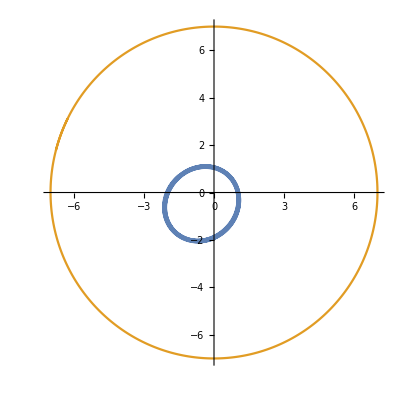

```mathematica
AA=1;M0=50;M1=1/100;M2=2;
Pc0={M0,0,0};
Pc1={M1,x1[t],y1[t]};
G=1;R1=1;R2=7;e1=0.4;V1=√((1+e1)(G M0)/R1);V2=AA √((G M0)/R2);Pc2={M2,R2 Cos[V2/R2 t],R2 Sin[V2/R2 t]};Per=600;result=NDSolve[{ x1''[t]==Ax[Pc1,Pc0]+Ax[Pc1,Pc2], y1''[t]==Ay[Pc1,Pc0]+Ay[Pc1,Pc2],x1[0]==R1,y1[0]==0,x1'[0]==0,y1'[0]==V1},{x1,y1},{t,0,Per},MaxSteps->400000];ParametricPlot[{Evaluate[{x1[t],y1[t]}/.result],Evaluate[{Pc2⟦2⟧,Pc2⟦3⟧}/.result]},{t,(Per-17),Per},AspectRatio->Automatic,PlotPoints->500,PlotRange->Automatic]
```